```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
(*Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
(*CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)*)*)

Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)
Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP Windows Vers.wl"];(*Configuration File*)
data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];

userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

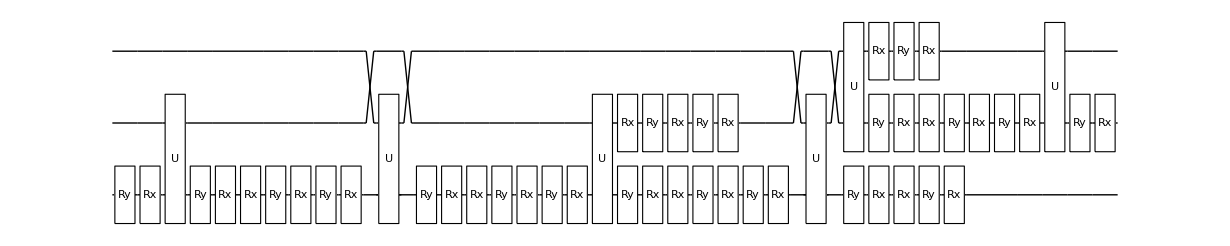

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}

Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]
```

```mathematica
Print[KetList[6][[1]]]
C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],,XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];

GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];
```

{0,0,0,0,0,0}

```mathematica
RenormList2Q=Table[{},{i,1,4}]

GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroverAlg6D3A2Q[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q},{j,1,8}]]]

GroverAlg6D3AVaryIt2Q[SearchSeed_]:=Flatten[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q}]
Init9=Table[Subscript[Init, i],{i,0,8}];

GroverDataUnNormCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{(*Init9,*)Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2Q[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,1}]
```

{{},{},{},{}}

{{{0.110682,0.0121231,0.0125151,0.00957611,0.0154035,0.0108619,0.0121805,0.00878431,0.0133054,0.0102066,0.0128852,0.00913497,0.0122829,0.0106101,0.0130244,0.00956541,0.0115462,0.00943396,0.0110804,0.00773283,0.0111297,0.00950699,0.0112758,0.00805285,0.0111706,0.00954543,0.0122116,0.00886241,0.0117164,0.0101258,0.012812,0.00950792,0.0124316,0.0103289,0.0112696,0.00801685,0.0115651,0.010013,0.0111983,0.0080004,0.0116736,0.0103091,0.0124425,0.00906588,0.0118919,0.0102818,0.0124674,0.00918228,0.0107223,0.00900029,0.0106137,0.00748161,0.0106371,0.00906829,0.0109148,0.00780226,0.0109531,0.00937298,0.0120503,0.00881417,0.011321,0.00970019,0.0124032,0.00921918},{0.220384,0.00566286,0.00664104,0.00585205,0.00858919,0.00628925,0.00637217,0.00630429,0.00689745,0.00645848,0.00579256,0.00574147,0.00627938,0.00639226,0.00594446,0.00580778,0.00635298,0.00631296,0.00608871,0.0060922,0.00616888,0.00640526,0.00600672,0.00600483,0.00602883,0.00655699,0.00566924,0.00561965,0.00605382,0.0062529,0.00582156,0.00560247,0.00583541,0.00589367,0.00621787,0.00615895,0.00599823,0.00627754,0.00627541,0.00625096,0.0058931,0.00621321,0.00571562,0.00564313,0.00619368,0.00633902,0.0060672,0.00589553,0.00587329,0.00631229,0.00600827,0.00602453,0.00608079,0.00642514,0.00597607,0.0059535,0.00594649,0.00637503,0.00553619,0.00545412,0.00604749,0.00624767,0.00580168,0.00558307},{0.290239,0.00300585,0.00376822,0.0022603,0.00617262,0.00292166,0.00310296,0.00224121,0.0041344,0.0026049,0.00382334,0.00266326,0.00332562,0.00247068,0.00317133,0.00237188,0.00333385,0.00245258,0.00312683,0.00212322,0.00299064,0.00217065,0.00285988,0.00201607,0.00288614,0.00232271,0.00350155,0.00260058,0.00306757,0.00246775,0.00318206,0.00241516,0.00389193,0.00296278,0.00303472,0.00217079,0.0030057,0.00247459,0.00268187,0.00190791,0.00302337,0.00275489,0.003602,0.00271107,0.00303201,0.00247361,0.00295288,0.00221962,0.00293589,0.00228386,0.00303904,0.00214661,0.00274405,0.00205443,0.0027898,0.00199446,0.00285094,0.00242666,0.00350765,0.00267825,0.00292624,0.00236962,0.00304722,0.00232212},{0.301908,0.000803976,0.00214275,0.000876829,0.00248334,0.00109128,0.00113494,0.00109694,0.00149606,0.00106748,0.000754423,0.000775151,0.0010229,0.000978097,0.000795528,0.000814635,0.00123309,0.00106036,0.000971331,0.000932461,0.000997487,0.00106787,0.000852202,0.000874785,0.000859841,0.00112051,0.000758802,0.000763158,0.000883888,0.000887217,0.000788439,0.000777947,0.000983251,0.000816395,0.00105011,0.000988313,0.000958578,0.00102017,0.000934987,0.000953721,0.000821049,0.000959881,0.000744421,0.000743057,0.000994241,0.000963838,0.000865595,0.000861473,0.000883779,0.0010667,0.000915064,0.000901857,0.000934093,0.00105657,0.000811523,0.000837407,0.000838836,0.00101667,0.000718532,0.000715856,0.000895434,0.000879378,0.00078936,0.000786785},{0.265385,0.000317281,0.000830112,0.000164564,0.00141577,0.000389313,0.000201006,0.000165462,0.0005452,0.000231707,0.000287158,0.000202295,0.000361403,0.000189158,0.000163351,0.000139684,0.000431037,0.000305931,0.000165647,0.000122587,0.000249632,0.000229514,0.000160446,0.000126274,0.000261882,0.000176254,0.000194321,0.000161325,0.000243611,0.000190098,0.000182648,0.000133448,0.000585149,0.000364354,0.000167848,0.000150983,0.000252447,0.000351505,0.000140246,0.000145307,0.000257741,0.000267152,0.000255778,0.000234981,0.000264387,0.000240978,0.000146274,0.0001267,0.000302889,0.000211901,0.000168854,0.000142024,0.000182047,0.000178321,0.000141968,0.000116783,0.000227667,0.000194963,0.000201993,0.000181441,0.000204561,0.00016983,0.000142732,0.00010708},{0.199277,0.000667622,0.0013668,0.000405872,0.000634457,0.000221281,0.000291629,0.000206187,0.000482401,0.000197135,0.000333242,0.000231692,0.000289921,0.000173146,0.000223292,0.000180742,0.000531291,0.000150979,0.000484896,0.000356019,0.000276928,0.000111514,0.000305475,0.000207258,0.000352109,0.000171134,0.000301278,0.000207319,0.000254323,0.000163882,0.000255936,0.000188246,0.000657882,0.000207957,0.000502387,0.000451245,0.000329914,0.000146993,0.00026151,0.000199696,0.000357541,0.000210844,0.000322568,0.000252292,0.000234852,0.000213576,0.000200071,0.0001755,0.000398379,0.000171281,0.000457464,0.000374319,0.000291934,0.000134769,0.00027866,0.000204788,0.000316336,0.000206126,0.000265644,0.000212787,0.000216078,0.0001559,0.000224726,0.000178304},{0.1286,0.00103419,0.000888162,0.000622739,0.000683179,0.000793328,0.000666269,0.000622626,0.000685174,0.000756023,0.000571633,0.000628704,0.000725921,0.000716897,0.000614363,0.000585567,0.000810443,0.000935702,0.000492474,0.000492582,0.000637328,0.000854926,0.000536767,0.000555604,0.000732835,0.000736574,0.000596398,0.000607688,0.000629417,0.000680634,0.000554195,0.000546284,0.000760493,0.000839916,0.000553773,0.000478654,0.000754572,0.000896285,0.000562481,0.00056546,0.000742445,0.000725065,0.000589909,0.000594505,0.000769195,0.00070985,0.000640111,0.000583199,0.000771883,0.000815231,0.000478743,0.000466571,0.000623874,0.000729086,0.000479081,0.00049442,0.000672583,0.000657574,0.000580085,0.000558023,0.000668012,0.000657106,0.000534582,0.000521902},{0.0683431,0.00151272,0.001765,0.00124834,0.000943678,0.000917089,0.000948788,0.000846741,0.00114043,0.000986737,0.00118031,0.000949718,0.00103746,0.00087662,0.00100051,0.000882789,0.00117848,0.00081519,0.00122566,0.00108251,0.00097472,0.000691323,0.00104767,0.000849578,0.00121855,0.000937445,0.00108439,0.000908055,0.0010331,0.000850023,0.00107346,0.000893962,0.00141443,0.000940799,0.00128052,0.00128535,0.00104263,0.000760106,0.00104458,0.000899817,0.0012012,0.000989162,0.00115553,0.000995058,0.000928658,0.000904537,0.000940505,0.000864165,0.00113549,0.000860567,0.00118981,0.00106892,0.00101937,0.000763339,0.00105257,0.000876547,0.00115069,0.000964945,0.00105956,0.000955986,0.000955684,0.000811219,0.00102205,0.000877326}}}

```mathematica
ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[KetList[6][[1]]],RydDev]]
```

{Rx_0[π],Deph_0[1.67785×10^-7],Rx_6[π],Deph_6[1.67785×10^-7],Rx_7[π],Deph_7[1.67785×10^-7],Rx_8[π],Deph_8[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[0.],Deph_8[0.],Ry_0[π/2],Deph_0[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_0[π/2],Deph_0[8.38926×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/4],Deph_0[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[7.90669×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Ry_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[9.08712×10^-8],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/4],Deph_0[4.19463×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Ry_1[π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π/2],Deph_1[8.38926×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Ry_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π],Deph_1[1.67785×10^-7],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[6.17984×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[9.08712×10^-8],Deph_1[9.08712×10^-8],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[π/4],Deph_2[4.19463×10^-8],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_0[π/4],Deph_0[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[6.17984×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Ry_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[6.17984×10^-7],Deph_8[6.17984×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[9.08712×10^-8],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[π/4],Deph_8[4.19463×10^-8],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_2[π/4],Deph_2[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[7.90669×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[0.],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],KrausNonTP_(8,4)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,4)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[7.90669×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[9.08712×10^-8],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/4],Deph_5[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[7.90669×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_5[-π/2],Deph_5[8.38926×10^-8],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[π/4],Deph_4[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π],Deph_4[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π],Deph_4[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[9.08712×10^-8],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[9.08712×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[π/4],Deph_4[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[7.90669×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/4],Deph_0[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[7.90669×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Ry_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[9.08712×10^-8],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/4],Deph_0[4.19463×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Ry_1[π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π/2],Deph_1[8.38926×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π],Deph_1[1.67785×10^-7],Rx_0[π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Ry_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[9.08712×10^-8],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Ry_6[π/2],Deph_6[8.38926×10^-8],Rx_0[π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[-π],Deph_1[1.67785×10^-7],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[6.17984×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Ry_1[π/2],Deph_1[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[-π],Deph_2[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[9.08712×10^-8],Deph_1[9.08712×10^-8],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Deph_0[7.90669×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[9.08712×10^-8],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Ry_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[6.17984×10^-7],Deph_8[1.05422×10^-6],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[9.08712×10^-8],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_3[π/4],Deph_3[4.19463×10^-8],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_2[π/4],Deph_2[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_3[π/4],Deph_3[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(7,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[9.08712×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[7.90669×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[5.27113×10^-7],Rx_7[-π/2],Deph_7[8.38926×10^-8],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],KrausNonTP_(7,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],KrausNonTP_(4,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[6.17984×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[6.17984×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[0.],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/4],Deph_5[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[7.90669×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_4[π/2],Deph_4[8.38926×10^-8],Rx_5[-π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[π/4],Deph_4[4.19463×10^-8],Ry_5[-π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[-π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(4,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],KrausNonTP_(5,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[9.08712×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/2],Deph_5[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Rx_4[π/2],Deph_4[8.38926×10^-8],Rx_5[-π],Deph_5[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π/2],Deph_4[8.38926×10^-8],Ry_5[π/4],Deph_5[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[2.63556×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_5[-π/2],Deph_5[8.38926×10^-8],Ry_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_5[-π/2],Deph_5[8.38926×10^-8],Rx_4[π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_5[-π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(5,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_5[-π/2],Deph_5[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_5[-π],Deph_5[1.67785×10^-7],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Ry_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Rx_5[π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_3[π/4],Deph_3[4.19463×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[9.08712×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Ry_3[-π/4],Deph_3[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_8[π/4],Deph_8[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_3[π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[6.17984×10^-7],Deph_8[0.],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_8[π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_2[-π],Deph_2[1.67785×10^-7],Rx_8[π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_2[π/2],Deph_2[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[7.90669×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[6.17984×10^-7],Deph_7[6.17984×10^-7],Deph_8[1.05422×10^-6],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Rx_7[π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[0.],Deph_8[1.05422×10^-6],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/4],Deph_0[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[7.90669×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Ry_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[9.08712×10^-8],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/4],Deph_0[4.19463×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Ry_1[π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π/2],Deph_1[8.38926×10^-8],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Ry_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π],Deph_1[1.67785×10^-7],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[6.17984×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[9.08712×10^-8],Deph_1[9.08712×10^-8],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[π/4],Deph_2[4.19463×10^-8],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_0[π/4],Deph_0[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[6.17984×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Ry_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[6.17984×10^-7],Deph_8[6.17984×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[9.08712×10^-8],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[π/4],Deph_8[4.19463×10^-8],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_2[π/4],Deph_2[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[7.90669×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[0.],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],KrausNonTP_(8,4)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,4)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[7.90669×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[9.08712×10^-8],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/4],Deph_5[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[7.90669×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_5[-π/2],Deph_5[8.38926×10^-8],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[π/4],Deph_4[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π],Deph_4[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π],Deph_4[1.67785×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[9.08712×10^-8],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[9.08712×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_4[π/4],Deph_4[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[π/4],Deph_8[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[9.08712×10^-8],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_8[π/2],Deph_8[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[7.90669×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[0.],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],KrausNonTP_(7,3)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_7[-π],Deph_7[1.67785×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/4],Deph_0[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[7.90669×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_0[π/4],Deph_0[4.19463×10^-8],Ry_1[-π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(0,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π/2],Deph_0[8.38926×10^-8],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[9.08712×10^-8],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[π/2],Deph_0[8.38926×10^-8],Rx_1[-π],Deph_1[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_0[-π/4],Deph_0[4.19463×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Rx_1[π/2],Deph_1[8.38926×10^-8],Deph_0[2.63556×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_0[-π/2],Deph_0[8.38926×10^-8],Ry_1[π/4],Deph_1[4.19463×10^-8],Deph_0[0.],Deph_1[2.63556×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π/2],Deph_1[8.38926×10^-8],Ry_0[π/2],Deph_0[8.38926×10^-8],Deph_0[0.],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Rx_0[π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[-π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_1[-π/2],Deph_1[8.38926×10^-8],Ry_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_1[-π],Deph_1[1.67785×10^-7],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[6.17984×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Ry_1[π/2],Deph_1[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[0.],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Ry_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_6[-π],Deph_6[1.67785×10^-7],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[6.17984×10^-7],Deph_8[1.05422×10^-6],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[9.08712×10^-8],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_3[π/4],Deph_3[4.19463×10^-8],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_2[π/4],Deph_2[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_3[π/4],Deph_3[4.19463×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(7,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[9.08712×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_7[-π],Deph_7[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[7.90669×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_7[π/4],Deph_7[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[2.63556×10^-7],Deph_8[5.27113×10^-7],Rx_7[-π/2],Deph_7[8.38926×10^-8],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[5.27113×10^-7],Ry_7[-π/2],Deph_7[8.38926×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_7[-π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[1.05422×10^-6],KrausNonTP_(7,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_7[-π/2],Deph_7[8.38926×10^-8],Ry_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_7[-π],Deph_7[1.67785×10^-7],KrausNonTP_(4,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[6.17984×10^-7],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[0.],Deph_8[6.17984×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[2.63556×10^-7],Deph_4[0.],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(4,5)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/4],Deph_5[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[7.90669×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_4[π/2],Deph_4[8.38926×10^-8],Rx_5[-π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_4[π/4],Deph_4[4.19463×10^-8],Ry_5[-π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π/2],Deph_4[8.38926×10^-8],Rx_5[-π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_4[-π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_4[-π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(4,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[0.],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_4[-π/2],Deph_4[8.38926×10^-8],KrausNonTP_(5,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[9.08712×10^-8],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[9.08712×10^-8],Rx_4[-π],Deph_4[1.67785×10^-7],Ry_5[-π/2],Deph_5[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Rx_4[π/2],Deph_4[8.38926×10^-8],Rx_5[-π],Deph_5[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Ry_4[-π/4],Deph_4[4.19463×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Rx_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[2.63556×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_4[-π/2],Deph_4[8.38926×10^-8],Ry_5[π/4],Deph_5[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[2.63556×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_5[-π/2],Deph_5[8.38926×10^-8],Ry_4[π/2],Deph_4[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[0.],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_5[-π/2],Deph_5[8.38926×10^-8],Rx_4[π],Deph_4[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[0.],Deph_5[5.27113×10^-7],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_5[-π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(5,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[0.],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_5[-π/2],Deph_5[8.38926×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_5[-π],Deph_5[1.67785×10^-7],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[6.17984×10^-7],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[6.17984×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Ry_5[π/2],Deph_5[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[0.],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Rx_5[π],Deph_5[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[0.],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/4],Deph_3[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[2.63556×10^-7],Deph_3[0.],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,8)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_8[-π/4],Deph_8[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[7.90669×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_3[π/4],Deph_3[4.19463×10^-8],Ry_8[-π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Ry_3[-π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[-π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(3,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[0.],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_3[-π/2],Deph_3[8.38926×10^-8],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[9.08712×10^-8],Deph_8[9.08712×10^-8],Rx_3[-π],Deph_3[1.67785×10^-7],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_3[π/2],Deph_3[8.38926×10^-8],Rx_8[-π],Deph_8[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[5.27113×10^-7],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[7.90669×10^-7],Deph_8[0.],Ry_3[-π/4],Deph_3[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_8[π/2],Deph_8[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[2.63556×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_3[-π/2],Deph_3[8.38926×10^-8],Ry_8[π/4],Deph_8[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[2.63556×10^-7],Rx_8[-π/2],Deph_8[8.38926×10^-8],Ry_3[π/2],Deph_3[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[0.],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Rx_3[π],Deph_3[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[0.],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[5.27113×10^-7],Rx_8[-π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],KrausNonTP_(8,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[0.],Ry_8[-π/2],Deph_8[8.38926×10^-8],Ry_7[-π/2],Deph_7[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[0.],Rx_8[-π],Deph_8[1.67785×10^-7],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[6.17984×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[6.17984×10^-7],Deph_8[0.],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_8[π],Deph_8[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[0.],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/4],Deph_2[4.19463×10^-8],Deph_0[2.63556×10^-7],Deph_1[2.63556×10^-7],Deph_2[0.],Deph_3[2.63556×10^-7],Deph_4[2.63556×10^-7],Deph_5[2.63556×10^-7],Deph_6[2.63556×10^-7],Deph_7[2.63556×10^-7],Deph_8[2.63556×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,6)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/4],Deph_6[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[7.90669×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_2[π/4],Deph_2[4.19463×10^-8],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_2[-π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_2[-π/2],Deph_2[8.38926×10^-8],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[9.08712×10^-8],Deph_7[9.08712×10^-8],Deph_8[5.27113×10^-7],Rx_2[-π],Deph_2[1.67785×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π/2],Deph_7[8.38926×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[5.27113×10^-7],Deph_8[1.05422×10^-6],Rx_2[π/2],Deph_2[8.38926×10^-8],Rx_6[-π],Deph_6[1.67785×10^-7],Ry_7[-π/4],Deph_7[4.19463×10^-8],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[7.90669×10^-7],Deph_8[1.05422×10^-6],Ry_2[-π/4],Deph_2[4.19463×10^-8],Rx_7[-π/2],Deph_7[8.38926×10^-8],Rx_6[π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[2.63556×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[5.27113×10^-7],Rx_2[-π/2],Deph_2[8.38926×10^-8],Ry_6[π/4],Deph_6[4.19463×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[2.63556×10^-7],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[-π/2],Deph_6[8.38926×10^-8],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[0.],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_2[π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(6,7)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[4.36241×10^-7],Deph_1[4.36241×10^-7],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[0.],Deph_7[0.],Deph_8[4.36241×10^-7],Ry_6[-π/2],Deph_6[8.38926×10^-8],Rx_7[π],Deph_7[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[5.27113×10^-7],Deph_7[0.],Deph_8[1.05422×10^-6],Rx_6[-π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Ry_6[-π/2],Deph_6[8.38926×10^-8],Deph_0[5.27113×10^-7],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[5.27113×10^-7],Deph_4[5.27113×10^-7],Deph_5[5.27113×10^-7],Deph_6[0.],Deph_7[5.27113×10^-7],Deph_8[5.27113×10^-7],Rx_6[π],Deph_6[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[0.],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}

```mathematica
RenormList2Q
```

{{0.731337,0.567899,0.44009,0.340553,0.263926,0.204939,0.159651,0.124716},{0.731212,0.568779,0.442098,0.343946,0.268104,0.209473,0.163994,0.128566},{0.731509,0.568659,0.44155,0.342713,0.266499,0.207621,0.162165,0.126877},{0.731385,0.5695,0.443563,0.346109,0.27077,0.212283,0.166675,0.1309}}

```mathematica
RenormDataVaryIt2Q=Table[{j,Mean[RenormList2Q[[All,j]]],StandardDeviation[RenormList2Q[[All,j]]]/Sqrt[8]},{j,1,8}]
GroverDataUnnormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]/2},{j,1,8}]
GroverData2ndHighestUnnormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]],{i,1,4}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]],{i,1,4}]]/2},{j,1,8}]

GroverDataRenormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]/2},{j,1,8}]
GroverData2ndHighestRenormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]]/RenormList2Q[[All,j]][[i]],{i,1,4}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]/RenormList2Q[[All,j]][[i]],{i,1,4}]]/2},{j,1,8}]
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{1,0.731361,0.0000434979},{2,0.568709,0.000231864},{3,0.441825,0.0005075},{4,0.34333,0.000821418},{5,0.267325,0.00101464},{6,0.208579,0.00109328},{7,0.163121,0.0010478},{8,0.127765,0.0009255}}

{{1,0.102431±0.00109194},{2,0.204304±0.00239151},{3,0.270491±0.00260184},{4,0.284158±0.00183611},{5,0.252622±0.00149937},{6,0.193299±0.00242099},{7,0.127702±0.00294039},{8,0.0706878±0.00293979}}

{{1,0.0136374±0.00047586},{2,0.00815066±0.0000301562},{3,0.00554029±0.00010064},{4,0.00246973±0.000053687},{5,0.00133669±0.0000469423},{6,0.000871923±0.000144365},{7,0.000975094±0.0000663837},{8,0.00160639±0.000038308}}

{{1,0.140056±0.00148488},{2,0.359247±0.00433389},{3,0.612235±0.00655908},{4,0.827703±0.00701828},{5,0.945059±0.00655092},{6,0.926714±0.0083535},{7,0.782677±0.0133071},{8,0.552857±0.0187537}}

{{1,0.0186465±0.000649826},{2,0.0143318±0.0000468169},{3,0.0125407±0.000248058},{4,0.00719213±0.000132591},{5,0.00499962±0.000167499},{6,0.00418976±0.00071875},{7,0.00597233±0.000370974},{8,0.0125751±0.000302221}}

{{1,0.268639±0.0000434979},{2,0.431291±0.000231864},{3,0.558175±0.0005075},{4,0.65667±0.000821418},{5,0.732675±0.00101464},{6,0.791421±0.00109328},{7,0.836879±0.0010478},{8,0.872235±0.0009255}}

```mathematica
RenormList=Table[{},{i,1,64}];
Init9=Table[Subscript[Init, i],{i,0,8}];
GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]
GroverDataUnNormCCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3AVaryIt[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}];

RenormDataVaryIt=Table[{j,Mean[RenormList[[All,j]]],StandardDeviation[RenormList[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverData2ndHighestUnnormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/8},{j,1,8}]
GroverDataRenormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]/8},{j,1,8}]
GroverData2ndHighestRenormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]]/RenormList[[All,j]][[i]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]/RenormList[[All,j]][[i]],{i,1,64}]]/8},{j,1,8}]
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
```

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[Init, 0]},RydDev,ReplaceAliases->True]]
```

{Damp_0[1],KrausNonTP_0[{{{0.996494,0},{0,1}}}],Deph_0[0.],Deph_1[0.000100661],Deph_2[0.000100661],Deph_3[0.000100661],Deph_4[0.000100661],Deph_5[0.000100661],Deph_6[0.000100661],Deph_7[0.000100661],Deph_8[0.000100661]}